```mathematica
ClearAll["Global`*"]
```

## Define edges

```mathematica
Simplices={{1,2,3,4,6},{1,2,3,5,6},{1,2,4,5,6},{1,3,4,5,6},{2,3,4,5,6}};
```

```mathematica
Tetrahedra=Flatten[Subsets[#,{4}]&/@Simplices,1];
```

```mathematica
BdFaces=Subsets[{1,2,3,4,5},{3}];
```

```mathematica
InternalFaces=Join[#,{6}]&/@Subsets[{1,2,3,4,5},{2}];
```

```mathematica
Triangles=Join[BdFaces,InternalFaces];
```

```mathematica
gaugefix={1,6,11,16,21};
```

```mathematica
InternalFacesEE={{{2,3},{12,13},{8,7}},{{2,4},{17,18},{9,7}},{{3,4},{17,19},{14,12}},{{8,9},{18,19},{14,13}},{{2,5},{22,23},{10,7}},{{3,5},{22,24},{15,12}},{{8,10},{23,24},{15,13}},{{4,5},{22,25},{20,17}},{{9,10},{23,25},{20,18}},{{14,15},{24,25},{20,19}}};
```

```mathematica
BDFacesEE={{{1,2},{7,6}},{{1,3},{12,11}},{{1,4},{17,16}},{{1,5},{22,21}},{{6,8},{13,11}},{{6,9},{18,16}},{{6,10},{23,21}},{{11,14},{19,16}},{{11,15},{24,21}},{{16,20},{25,21}}};
```

```mathematica
ConnectionEE={{2,7},{3,12},{4,17},{5,22},{8,13},{9,18},{10,23},{14,19},{15,24},{20,25}};
```

```mathematica
EE=Join[Flatten[InternalFacesEE,1],Flatten[BDFacesEE,1]];
```

```mathematica
GaugeTetra={2,3,4,5,7,8,9,10,12,13,14,15,17,18,19,20,22,23,24,25};
```

```mathematica
error=1000;
```

```mathematica
ls16i0=2.008276000000000124391164035841941303361952661563081705308050220275782604684167154118767939507961273;
ls26i0=6.65857777295881130644656794617358870524278621920225872777029586964663704362621388099796604365110397;
ls36i0=4.72025131058747846455187061967409036038794807782193641695735499810761964800676082631980534642934799;
ls46i0=0.540326307979470575296978730807150099043190440376768076920860878453170203505884217065613484010100365;
ls56i0=6.19493539080728552198801493547536651880440801499390948767725190106294558267663319384155329316854477;
lsi0=SetPrecision[{ls16i0,ls26i0,ls36i0,ls46i0,ls56i0},error];
```

## Define function for tetnormals

```mathematica
Vertex5=SetPrecision[{{0,0,0,0},{0,-((2 √10)/3^(3/4)),-((√5)/3^(3/4)),-((√5)/3^(1/4))},{0,0,0,-((2 √5)/3^(1/4))},{-(1/(3^(1/4) √10)),-((√(5/2))/3^(3/4)),-((√5)/3^(3/4)),-((√5)/3^(1/4))},{0,0,-3^(1/4) √5,-((√5)/3^(1/4))}}//N,error];
```

```mathematica
distance[V_,i_,j_]:=Block[{ge},ge=DiagonalMatrix[{-1,1,1,1}];(V⟦i⟧-V⟦j⟧).ge.(V⟦i⟧-V⟦j⟧)]
```

```mathematica
Heron2[a_,b_,c_]:=(a+b+c)/2((a+b+c)/2-a)((a+b+c)/2-b)((a+b+c)/2-c)
```

```mathematica
CenterT[tet_]:= Total[tet]/Length[tet]
```

```mathematica
η=DiagonalMatrix[{-1,1,1,1}];
```

```mathematica
Vertex[vert_,lsi_]:=Block[{v6,t6,x6,y6,z6,Vertex66,sub,eqns,vertexNum},v6={t6,x6,y6,z6};
Vertex66=Join[Vertex5,{v6}];
sub=Subsets[{1,2,3,4,5},{4}];
vertexNum=sub[[vert]];
eqns=Table[distance[Vertex66,vertexNum[[i]],6]==lsi[[vertexNum[[i]]]],{i,4}];
zz={t6,x6,y6,z6}/.Solve[eqns,{t6,x6,y6,z6},WorkingPrecision->error]//Quiet;
If[vert==4,Join[Vertex5,{zz[[2]]}],Join[Vertex5,{zz[[1]]}]]
]
```

```mathematica
lsi=Block[{v1,v2},v1=SetPrecision[Vertex[1,lsi0]//N,error];v2=SetPrecision[Vertex[2,lsi0]//N,error];{distance[v1,1,6],distance[v1,2,6],distance[v1,3,6],distance[v1,4,6],distance[v2,5,6]}];
```

## Test length, Areas and Volumes

### Test length

```mathematica
Vertex6=Vertex[1,lsi];
```

```mathematica
dis2D=Table[distance[Vertex6,i,j],{i,1,6},{j,i+1,6}]//Flatten//N;
```

```mathematica
#>0&/@dis2D
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
{ls16,ls25,ls36,ls46,ls56}={distance[Vertex6,1,6],distance[Vertex6,2,6],distance[Vertex6,3,6],distance[Vertex6,4,6],distance[Vertex6,5,6]};
```

```mathematica
dis2D
```

{11.547,11.547,4.27239,11.547,2.00828,11.547,4.27239,11.547,6.65858,4.27239,11.547,4.72025,4.27239,0.540326,6.19494}

### Test areas

```mathematica
AreaTriangle[{x1_,x2_,x3_}]:=Module[{l1,l2,tarea}, l1=x1-x2; l2=x1-x3; tarea=1/2Sqrt[(l1.η.l1)(l2.η.l2) -(l1.η.l2)^2]; Return[tarea]]
```

```mathematica
Aij=Vertex6[[#]]&/@Join[BdFaces,InternalFaces];
Areas=AreaTriangle[#]&/@Aij//N;
#>0&/@Areas
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Areas
```

{5.,2.,5.,2.,5.,2.,2.,5.,2.,2.,1.68066,0.958532,0.292516,1.55289,2.80282,0.603466,3.19463,0.759333,2.69916,0.676545}

### Test tetrahedra volumes

```mathematica
CM3D[ls12_,ls13_,ls14_,ls23_,ls24_,ls34_]:=({{0, ls12, ls13, ls14, 1}, {ls12, 0, ls23, ls24, 1}, {ls13, ls23, 0, ls34, 1}, {ls14, ls24, ls34, 0, 1}, {1, 1, 1, 1, 0}})
```

```mathematica
V3sq[{ls12_,ls13_,ls14_,ls23_,ls24_,ls34_}]:=-(-1)^3/(2^3(3!)^2)Det[CM3D[ls12,ls13,ls14,ls23,ls24,ls34]]
```

```mathematica
lij3D=Subsets[#,{2}]&/@Tetrahedra;
dist3D=Table[distance[Vertex6,lij3D⟦i,j,1⟧,lij3D⟦i,j,2⟧],{i,Length[lij3D]},{j,6}]//N;
vol3D=V3sq[#]&/@dist3D;
#>0&/@vol3D
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Test 4-simplex volumes

```mathematica
CM4D[ls12_,ls13_,ls14_,ls15_,ls23_,ls24_,ls25_,ls34_,ls35_,ls45_]:=({{0, ls12, ls13, ls14, ls15, 1}, {ls12, 0, ls23, ls24, ls25, 1}, {ls13, ls23, 0, ls34, ls35, 1}, {ls14, ls24, ls34, 0, ls45, 1}, {ls15, ls25, ls35, ls45, 0, 1}, {1, 1, 1, 1, 1, 0}})
```

```mathematica
V4sq[{ls12_,ls13_,ls14_,ls15_,ls23_,ls24_,ls25_,ls34_,ls35_,ls45_}]:=-(-1)^4/(2^4(4!)^2)Det[CM4D[ls12,ls13,ls14,ls15,ls23,ls24,ls25,ls34,ls35,ls45]]
```

```mathematica
lij4D=Subsets[#,{2}]&/@Simplices;
dist4D=Table[distance[Vertex6,lij4D⟦i,j,1⟧,lij4D⟦i,j,2⟧],{i,Length[lij4D]},{j,10}]//N;
vol4D=V4sq[#]&/@dist4D;
#<0&/@vol4D
```

{True,True,True,True,True}

## From Length to Vertex

```mathematica
Tetnormal[{x1_,x2_,x3_,x4_},c_]:= Block[{l1,l2,l3,nn,norm},l1=x1-x2; l2=x1-x3;l3=x1-x4; nn=LeviCivitaTensor[4].(η.l1).(η.l2).(η.l3); norm = Sqrt[-nn.η.nn] ;
If[Refine[nn.(η.(x1-c))>0],Return[nn/norm],Return[-nn/norm]];
]
```

```mathematica
To3D[n_]:=Rest[n]
```

```mathematica
T={1,0,0,0};
```

```mathematica
Boost[N_,ref_]:=If[N⟦1⟧>0,η+ 1/(1-N.η.ref)(N⊗N+N⊗ref+ref⊗ref)-(1-2N.η.ref)/(1-N.η.ref)(ref⊗N),-(η+ 1/(1+N.η.ref)(N⊗N-N⊗ref+ref⊗ref)-(1+2N.η.ref)/(1+N.η.ref)(-ref⊗N))]
```

```mathematica
ξ[{x_,y_,z_}]:=1/(√2){{√(1+z)},{(x+I*y)/(√(1+z))}}
```

```mathematica
TetnormalRotate[ls_,n_]:=Block[{i,vert,vertices,simplexCoord,FScenter,tetrahedran,tetnormals,timelikeNorm,tetraRef,TetNormalsref,ref,refCoord,refNormal,Λ0},
i=If[Mod[n,5]==0,Quotient[n,5],Quotient[n,5]+1];

vert=Simplices⟦i⟧;
vertices=Vertex[i,ls];
simplexCoord=vertices[[#]]&/@vert;
FScenter=CenterT[simplexCoord];

tetrahedran=vertices⟦#⟧&/@Tetrahedra⟦n⟧;
tetnormals=Tetnormal[tetrahedran,FScenter];

ref=Which[i==1,2,i==2,6,i==3,13,i==4,18,i==5,23];

tetraRef=vertices⟦#⟧&/@Tetrahedra⟦ref⟧;
TetNormalsref=Tetnormal[tetraRef,FScenter];
Λ0=-Boost[TetNormalsref,T];

If[tetnormals.η.tetnormals<0&&tetnormals∈Reals,Λ0.η.tetnormals,0]

]
```

```mathematica
CheckCondition[ls_,i_]:=Block[{faceCoor,triangles,vertices,checkAreas,check1,seg,length,vol,checknormals},
triangles=Subsets[Simplices⟦i⟧,{3}];
vertices=Vertex[i,ls];
faceCoor=vertices[[#]]&/@triangles;
checkAreas=AreaTriangle[#]&/@faceCoor;
check1=If[Total[Boole[#>0&/@checkAreas]]==Length[checkAreas]&&(checkAreas∈Reals),1,0];

seg=Subsets[Simplices⟦i⟧,{2}];
length=If[check1==1,Table[distance[vertices,seg⟦k,1⟧,seg⟦k,2⟧],{k,Length[seg]}],0];

vol=Subsets[Simplices⟦i⟧,{4}];
checknormals=If[Total[Boole[#>0&/@length]]==Length[length],Table[TetnormalRotate[ls,k],{k,5i-4,5i}],0];
If[checknormals∈Reals&&Total[(#.η.#)&/@checknormals]==-Length[checknormals],1,0]

]
```

```mathematica
kappa[n_,m_]:=Block[{kappa1,kappa2,kappa3,kappa4,kappa5,i,output},
i=If[Mod[n,5]==0,Quotient[n,5],Quotient[n,5]+1];

kappa1=If[n<m,1,-1];

kappa2=If[(n==7&&m==6)||(n==6&&m==8)||(n==6&&m==9)||(n==6&&m==10)||(n==8&&m==7)||(n==8&&m==9)||(n==8&&m==10)||(n==9&&m==7)||(n==10&&m==7)||(n==9&&m==10),1,-1];

kappa3=If[(n==12&&m==11)||(n==12&&m==13)||(n==14&&m==12)||(n==15&&m==12)||(n==13&&m==11)||(n==14&&m==13)||(n==15&&m==13)||(n==11&&m==14)||(n==11&&m==15)||(n==14&&m==15),1,-1];

kappa4=If[(n==17&&m==16)||(n==17&&m==18)||(n==17&&m==19)||(n==20&&m==17)||(n==18&&m==16)||(n==18&&m==19)||(n==20&&m==18)||(n==19&&m==16)||(n==20&&m==19)||(n==16&&m==20),1,-1];

kappa5=If[(n==22&&m==21)||(n==22&&m==23)||(n==22&&m==24)||(n==22&&m==25)||(n==23&&m==21)||(n==23&&m==24)||(n==23&&m==25)||(n==24&&m==21)||(n==24&&m==25)||(n==25&&m==21),1,-1];

output=Which[i==1,kappa1,i==2,kappa2,i==3,kappa3,i==4,kappa4,i==5,kappa5]
]
```

```mathematica
BoundaryDataRotate[ls_,n_,m_]:=Block[{i,TetNormalsM,TetNormalsN,triangleNM,vertices,TriangleCoord,Λ,Arv,Nab,nab,xv},
i=If[Mod[n,5]==0,Quotient[n,5],Quotient[n,5]+1];

TetNormalsN=TetnormalRotate[ls,n];

TetNormalsM=TetnormalRotate[ls,m];

triangleNM=Intersection[Tetrahedra⟦n⟧,Tetrahedra⟦m⟧];

vertices=Vertex[i,ls];
TriangleCoord=vertices[[#]]&/@triangleNM;

Λ=Boost[TetNormalsN,T];
Arv=AreaTriangle[TriangleCoord];

Nab= (TetNormalsM+TetNormalsN (TetNormalsM.η.TetNormalsN ) )/Sqrt[(TetNormalsM.η.TetNormalsN ) ^2-1];

nab=kappa[n,m]*To3D[Λ.η.Nab];
xv=ξ[nab];
If[N[Λ.η.Nab]⟦1⟧==0,{Arv,nab,xv},0]
]
```

```mathematica
dihedralAngle[ls_,n_,m_]:=Block[{TetNormalsN,TetNormalsM,sign},

TetNormalsN=TetnormalRotate[ls,n];
TetNormalsM=TetnormalRotate[ls,m];

sign=If[Sign[TetNormalsN⟦1⟧]==Sign[TetNormalsM⟦1⟧],-1,1];
sign*Re[ArcCosh[TetNormalsN.η.TetNormalsM]]
]
```

```mathematica
DeficitAngles[lsx_,i_]:=dihedralAngle[lsx,InternalFacesEE⟦i,1,1⟧,InternalFacesEE⟦i,1,2⟧]+dihedralAngle[lsx,InternalFacesEE⟦i,2,1⟧,InternalFacesEE⟦i,2,2⟧]+dihedralAngle[lsx,InternalFacesEE⟦i,3,1⟧,InternalFacesEE⟦i,3,2⟧]
```

## critical points

```mathematica
g[nab_,θ_]:=Cosh[θ/2]PauliMatrix[0]+Sinh[θ/2]nab.{PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]}
```

```mathematica
group[ls_,n_]:=Block[{i,ref,nab,nabx,theta,nab0,g1,g0},

i=If[Mod[n,5]==0,Quotient[n,5],Quotient[n,5]+1];

ref=Which[i==1,2,i==2,6,i==3,13,i==4,18,i==5,23];

g0=Which[ref==6,IdentityMatrix[2],
ref==2,nab=BoundaryDataRotate[ls,6,7]⟦2⟧;
theta=dihedralAngle[ls,6,7];g[nab,-theta],
ref==13,nab=BoundaryDataRotate[ls,6,8]⟦2⟧;
theta=dihedralAngle[ls,6,8];g[nab,theta],
ref==18,nab=BoundaryDataRotate[ls,6,9]⟦2⟧;
theta=dihedralAngle[ls,6,9];g[nab,theta],
ref==23,nab=BoundaryDataRotate[ls,6,10]⟦2⟧;
theta=dihedralAngle[ls,6,10];g[nab,theta]];

g1=If[n==ref,g0,nab=BoundaryDataRotate[ls,ref,n][[2]];
theta=dihedralAngle[ls,ref,n];g0.g[nab,If[n≠1&&n≠7&&n≠11&&n≠16&&n≠19&&n≠22,theta,-theta]]];

If[i==3||i==4,g1,ConjugateTranspose[Inverse[g1]]]
]
```

#### Spinor z

```mathematica
BDdata1[ls_]:=Block[{},
 
Do[xv[EE[[i,1]],EE[[i,2]]]=BoundaryDataRotate[ls,EE[[i,1]],EE[[i,2]]][[3]],{i,Length[EE]}];

Do[xv[EE[[i,2]],EE[[i,1]]]=BoundaryDataRotate[ls,EE[[i,2]],EE[[i,1]]][[3]],{i,Length[EE]}];

Do[nab[EE⟦i,2⟧,EE⟦i,1⟧]=BoundaryDataRotate[ls,EE⟦i,2⟧,EE⟦i,1⟧]⟦2⟧,{i,Length[EE]}];

Do[nab[EE⟦i,1⟧,EE⟦i,2⟧]=BoundaryDataRotate[ls,EE⟦i,1⟧,EE⟦i,2⟧]⟦2⟧,{i,Length[EE]}];

Do[Arv[EE⟦i,1⟧,EE⟦i,2⟧]=BoundaryDataRotate[ls,EE⟦i,1⟧,EE⟦i,2⟧]⟦1⟧,{i,Length[EE]}];
Do[Arv[EE⟦i,2⟧,EE⟦i,1⟧]=BoundaryDataRotate[ls,EE⟦i,2⟧,EE⟦i,1⟧]⟦1⟧,{i,Length[EE]}];
]
```

```mathematica
SO3ToSU2[so3_]:=Block[{el,su2},el=EulerAngles[so3];
su2=Table[WignerD[{1/2,m1,m2},el[[1]],el[[2]],el[[3]]],{m1,-1/2,1/2},{m2,-1/2,1/2}]]
```

```mathematica
hsu2[n_]:=Block[{i,faces,temp,ii,facetemp,so3,xx0,sv,sv0,eqs2,a,xx,su22,su2,sol,eqs},

i=Quotient[n,5,1]+1;
faces=DeleteCases[Table[j,{j,5 i-4,5 i}],n];

temp=Which[n==7,2,n==12,3,n==13,8,n==18,9,n==19,14,n==24,15,n==25,20,n==17,4,n==22,5,n==10,23,True,n];
ii=Quotient[temp,5,1]+1;
facetemp=DeleteCases[Table[j,{j,5 ii-4,5 ii}],temp];

xx0={};
xx={};
sv0={};
sv={};
Table[Table[If[Intersection[Tetrahedra⟦n⟧,Tetrahedra⟦faces⟦i⟧⟧]==Intersection[Tetrahedra⟦temp⟧,Tetrahedra⟦facetemp⟦j⟧⟧],AppendTo[xx,nab[temp,facetemp⟦j⟧]];AppendTo[xx0,nab[n,faces⟦i⟧]];AppendTo[sv,xv[temp,facetemp⟦j⟧]];AppendTo[sv0,xv[n,faces⟦i⟧]],Unevaluated[Sequence[]]],{j,4}],{i,4}];
so3=(RotationMatrix[a,{xx0[[1]],xx[[1]]}]/.Solve[(RotationMatrix[a,{xx0[[1]],xx[[1]]}].xx0[[2]])[[1]]==xx[[2,1]],a,WorkingPrecision->error])//Quiet;

If[Length[so3]==1,su2=SO3ToSU2[so3[[1]]];
eqs=su2.sv0[[-1]]/sv[[-1]]//N//Chop;If[eqs[[1]]==eqs[[2]],su2,"Wrong"],su2=SO3ToSU2[so3[[1]]];
eqs=su2.sv0[[-1]]/sv[[-1]]//N//Chop;su22=SO3ToSU2[so3[[2]]];
eqs2=su22.sv0[[-1]]/sv[[-1]]//N//Chop;Which[eqs[[1]]==eqs[[2]],su2,eqs2[[1]]==eqs2[[2]],su22,True,"Wrong2"]]
]
```

```mathematica
BDdata1[lsi]
```

```mathematica
Sl2cToSu2[{{a_,c_},{b_,d_}}]:=Block[{λ,u,v,mu,upper,su2},λ=Sqrt[Abs[b]^2+Abs[d]^2];u=b/λ;v=d/λ;
mu=a*Conjugate[u]+c*Conjugate[v];
upper={{λ^-1,mu},{0,λ}};
su2={{Conjugate[v],-Conjugate[u]},{u,v}};
{upper,su2}]
```

```mathematica
GaugeGroup[ls_,n_]:=Block[{i,temp,gvn0,sl2c,gvn,xvnm,nn,gvnn},
i=Quotient[n,5,1]+1;
temp=Which[n==7,2,n==12,3,n==13,8,n==18,9,n==19,14,n==24,15,n==25,20,n==4,17,n==5,22,n==10,23,True,n];
gvn0=group[ls,temp].Inverse[hsu2[temp]];
sl2c=Sl2cToSu2[gvn0];
gvn=sl2c[[1]];
nn=Which[temp==2,7,temp==3,12,temp==8,13,temp==9,18,temp==14,19,temp==15,24,temp==17,4,temp==20,25,temp==22,5,temp==23,10];
gvnn=group[ls,nn].Inverse[hsu2[nn]].Inverse[sl2c[[2]]];
{Which[n==2||n==3||n==8||n==9||n==14||n==15||n==17||n==20||n==22||n==23,gvn,n==7||n==12||n==13||n==18||n==19||n==24||n==25||n==4||n==5||n==10,gvnn],sl2c[[2]]}]
```

```mathematica
spinor[ls_,n_,m_]:=Block[{gvx},
gvx=Chop[gv[n],10^-50];
(Inverse[ConjugateTranspose[gvx]].xi[n,m])/(Inverse[ConjugateTranspose[gvx]].xi[n,m])[[1,1]]]
```

```mathematica
BDdata2[ls_]:=Block[{},

Do[If[MemberQ[GaugeTetra,i],gv[i]=GaugeGroup[ls,i][[1]],gv[i]=group[ls,i].Inverse[hsu2[i]]],{i,1,25}];

Do[xi[EE[[i,1]],EE[[i,2]]]=If[MemberQ[GaugeTetra,EE[[i,1]]],GaugeGroup[ls,EE[[i,1]]][[2]].hsu2[EE[[i,1]]].xv[EE[[i,1]],EE[[i,2]]],hsu2[EE[[i,1]]].xv[EE[[i,1]],EE[[i,2]]]],{i,Length[EE]}];

Do[xi[EE[[i,2]],EE[[i,1]]]=If[MemberQ[GaugeTetra,EE[[i,2]]],GaugeGroup[ls,EE[[i,2]]][[2]].hsu2[EE[[i,2]]].xv[EE[[i,2]],EE[[i,1]]],hsu2[EE[[i,2]]].xv[EE[[i,2]],EE[[i,1]]]],{i,Length[EE]}];    

Do[If[MemberQ[GaugeTetra,i],su2[i]=GaugeGroup[ls,i][[2]],su2[i]=IdentityMatrix[2]],{i,25}];

Do[zv[EE⟦i,1⟧,EE⟦i,2⟧]=spinor[ls,EE⟦i,1⟧,EE⟦i,2⟧],{i,Length[EE]}];
]
```

## check the critical points equations

```mathematica
BDdata2[lsi];
```

```mathematica
closureCondition=Table[Sum[kappa[i,j]*Arv[i,j]*nab[i,j],{j,21,i-1}]+Sum[kappa[i,j]*Arv[i,j]*nab[i,j],{j,i+1,25}],{i,21,25}]
```

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

```mathematica
Map[#⟦1⟧-#⟦2⟧&,Table[Inverse[ConjugateTranspose[gv[EE⟦j,1⟧]]].xi[EE⟦j,1⟧,EE⟦j,2⟧]/Inverse[ConjugateTranspose[gv[EE⟦j,2⟧]]].xi[EE⟦j,2⟧,EE⟦j,1⟧],{j,1,50}]]
```

{{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ}}

```mathematica
Map[#⟦1⟧-#⟦2⟧&,Table[gv[EE⟦j,1⟧].xi[EE⟦j,1⟧,EE⟦j,2⟧]/gv[EE⟦j,2⟧].xi[EE⟦j,2⟧,EE⟦j,1⟧],{j,1,50}]]
```

{{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ}}

```mathematica
Map[#⟦1⟧-#⟦2⟧&,Table[ConjugateTranspose[gv[BDFacesEE[[i,1,2]]]].zv[BDFacesEE[[i,1,1]],BDFacesEE[[i,1,2]]]/ConjugateTranspose[gv[BDFacesEE[[i,2,1]]]].zv[BDFacesEE[[i,2,1]],BDFacesEE[[i,2,2]]],{i,Length[BDFacesEE]}]]
```

{{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ}}

```mathematica
Map[#⟦1⟧-#⟦2⟧&,Table[ConjugateTranspose[gv[InternalFacesEE[[i,1,2]]]].zv[InternalFacesEE[[i,1,1]],InternalFacesEE[[i,1,2]]]/ConjugateTranspose[gv[InternalFacesEE[[i,2,1]]]].zv[InternalFacesEE[[i,2,1]],InternalFacesEE[[i,2,2]]],{i,Length[InternalFacesEE]}]]
```

{{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ}}

```mathematica
Map[#⟦1⟧-#⟦2⟧&,Table[ConjugateTranspose[gv[InternalFacesEE[[i,2,2]]]].zv[InternalFacesEE[[i,2,1]],InternalFacesEE[[i,2,2]]]/ConjugateTranspose[gv[InternalFacesEE[[i,3,1]]]].zv[InternalFacesEE[[i,3,1]],InternalFacesEE[[i,3,2]]],{i,Length[InternalFacesEE]}]]
```

{{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ}}

```mathematica
Map[#⟦1⟧-#⟦2⟧&,Table[ConjugateTranspose[gv[InternalFacesEE[[i,3,2]]]].zv[InternalFacesEE[[i,3,1]],InternalFacesEE[[i,3,2]]]/ConjugateTranspose[gv[InternalFacesEE[[i,1,1]]]].zv[InternalFacesEE[[i,1,1]],InternalFacesEE[[i,1,2]]],{i,Length[InternalFacesEE]}]]
```

{{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ}}

```mathematica
Map[#⟦1⟧-#⟦2⟧&,Table[ConjugateTranspose[gv[InternalFacesEE[[i,3,2]]]].zv[InternalFacesEE[[i,3,1]],InternalFacesEE[[i,3,2]]]/ConjugateTranspose[gv[InternalFacesEE[[i,1,1]]]].zv[InternalFacesEE[[i,1,1]],InternalFacesEE[[i,1,2]]],{i,Length[InternalFacesEE]}]]
```

{{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ}}

```mathematica
InternalFaces
```

{{1,2,6},{1,3,6},{1,4,6},{1,5,6},{2,3,6},{2,4,6},{2,5,6},{3,4,6},{3,5,6},{4,5,6}}

```mathematica
InternalFacesEE
```

{{{2,3},{12,13},{8,7}},{{2,4},{17,18},{9,7}},{{3,4},{17,19},{14,12}},{{8,9},{18,19},{14,13}},{{2,5},{22,23},{10,7}},{{3,5},{22,24},{15,12}},{{8,10},{23,24},{15,13}},{{4,5},{22,25},{20,17}},{{9,10},{23,25},{20,18}},{{14,15},{24,25},{20,19}}}

```mathematica
EE
```

{{2,3},{12,13},{8,7},{2,4},{17,18},{9,7},{3,4},{17,19},{14,12},{8,9},{18,19},{14,13},{2,5},{22,23},{10,7},{3,5},{22,24},{15,12},{8,10},{23,24},{15,13},{4,5},{22,25},{20,17},{9,10},{23,25},{20,18},{14,15},{24,25},{20,19},{1,2},{7,6},{1,3},{12,11},{1,4},{17,16},{1,5},{22,21},{6,8},{13,11},{6,9},{18,16},{6,10},{23,21},{11,14},{19,16},{11,15},{24,21},{16,20},{25,21}}

```mathematica
xi[EE⟦1,1⟧,EE⟦1,2⟧]
```

{{0.50562190456740949129758339701201018838317403932310858640568779391838616870224851369418291639510092849672542048587018097450331965527168522558584725642184739630589715928188810633816019040917322477335408351418204843733909390541495546505090093571013867694011117386623253569746936548433242721091184127059269777000523882070037876920794111054300965780235121848429729715560315407961003660053781433955912993197181574202791142168923194612663367659183130708436529098620696126402486+0.01465179526211706610468698792708601700306960371498790886051162319924438838521009684580597540603202161810153121257656045031267120651869124121435905163314532452071063052591846929209686034266366389841916587728439401663942203100345376962454547825770453267442020985461739683820302550087006124135006526300255553898403521803939423108154152791275583662527587980864875570453653506875007669623827906448550972084485406077636596743674401781860355398964919866642393061887965108285065 ⅈ},{-0.12864147264082554955546291326654774038575509421026378487144922173548788887003964614884749871839223034386255479988083487942814135124301527349452348863529591298772651735645791527896861085719601537799575105275325804256884944680248080313030446251534902079681449226483583635640109995708013006395007409656168597255657289460507194557005082378534137296620670616638569243349769258483689009035044002260127552556907859686616891458479296829733953047944933678875914188299969037542949+0.852984868584444576667926971308176840323983770336570316548225659923826270475602342375485304198700868092774988435018760716509022827030041643937689703213108272249070612986391499836969423467294847097526287183196137100962189270266853353375518299378157659757097868368016790528989172685365464139234765322020628622591003444370647078168277537294824951307128111900562254382623728248834586904886128506889044547497181790192275351719706993054597322386739799107204973205391045551566468 ⅈ}}

```mathematica
N[Arv[4,#]&/@{5},2]
```

{0.76}

```mathematica
0.71
```

0.71

## action

```mathematica
ExpM[z_List]:=Block[{z1,z2,z3,out},If[Length[z]==6,
z1=1+(z⟦1⟧+I z⟦2⟧)/Sqrt[2];z2=(z⟦3⟧+I z⟦4⟧)/Sqrt[2];z3=(z⟦5⟧+I z⟦6⟧)/Sqrt[2];out={{z1,z2},{z3,(1+z2 z3)/z1}},
z1=1+z⟦1⟧/Sqrt[2];z2=(z⟦2⟧+I z⟦3⟧)/Sqrt[2];z3=z3=1/(1+z⟦1⟧/Sqrt[2]);out={{z1,z2},{0,z3}}]
]
```

```mathematica
ExpMconj[z_List]:=Block[{z1,z2,z3,out},If[Length[z]==6,z1=1+(z⟦1⟧-I z⟦2⟧)/Sqrt[2];z2=(z⟦3⟧-I z⟦4⟧)/Sqrt[2];z3=(z⟦5⟧-I z⟦6⟧)/Sqrt[2];out={{z1,z2},{z3,(1+z2 z3)/z1}},
z1=1+z⟦1⟧/Sqrt[2];z2=(z⟦2⟧-I z⟦3⟧)/Sqrt[2];z3=1/(1+z⟦1⟧/Sqrt[2]);out={{z1,z2},{0,z3}}]]
```

```mathematica
LogM[z_]:=Log[z Exp[-I*(1/2*Pi)]]+I*1/2*Pi;
```

```mathematica
Feb1[{e1_,e2_},{zx_,zy_},ge2_List,γ_]:=Block[{gv1e2,zv1bconj,Zv1e2bLeft,Zv1e2bXie2b,gv1e2conj,zv1b,Zv1e2bRight,ZveZve,areas,output},
gv1e2=gv[e2].ExpM[ge2];
zv1bconj={{1},{Conjugate[zv[e1,e2][[2,1]]]+zx-I*zy}};
Zv1e2bLeft=(Transpose[zv1bconj].gv1e2);
Zv1e2bXie2b=Zv1e2bLeft.xi[e2,e1];

gv1e2conj=Transpose[ExpMconj[ge2]].ConjugateTranspose[gv[e2]];
zv1b={{1},{zv[e1,e2][[2,1]]+zx+I*zy}};
Zv1e2bRight=gv1e2conj.zv1b;
ZveZve=Sqrt[Zv1e2bLeft.Zv1e2bRight];

areas=Arv[e1,e2];

output=Flatten[2*areas*LogM[Zv1e2bXie2b/ZveZve]+I *γ*areas*LogM[ZveZve^2]]⟦1⟧
]
```

```mathematica
Feb2[{e3_,e4_},{zx_,zy_},ge3_List,γ_]:=Block[{gv2e3conj,zv2b,Zv1e2bRight,Xie3bZv2e3b,gv2e3,zv2bconj,Zv2e3bLeft,Zv2e3Zv2e3,areas,output},
gv2e3conj=Transpose[ExpMconj[ge3]].ConjugateTranspose[gv[e3]];
zv2b={{1},{zv[e3,e4][[2,1]]+zx+I*zy}};
Zv1e2bRight=gv2e3conj.zv2b;
Xie3bZv2e3b=ConjugateTranspose[xi[e3,e4]].Zv1e2bRight;

gv2e3=gv[e3].ExpM[ge3];
zv2bconj={{1},{Conjugate[zv[e3,e4][[2,1]]]+zx-I*zy}};
Zv2e3bLeft=(Transpose[zv2bconj].gv2e3);
Zv2e3Zv2e3=Sqrt[Zv2e3bLeft.Zv1e2bRight];

areas=Arv[e3,e4];

output=Flatten[2*areas*LogM[Xie3bZv2e3b/Zv2e3Zv2e3]-I *γ*areas*LogM[Zv2e3Zv2e3^2]]⟦1⟧
]
```

```mathematica
Fex[{ve1_,ve2_},{vpe2_,vpe3_},j_,{zx_,zy_},{zpx_,zpy_},gve2_List,gvpe2_List,γ_]:=Block[{gvpeconj,zvp,ZvpxRight,gvpe,zvpconj,ZvpxLeft,gve2x,zvxconj,ZvxLeft,gveconj,zvx,ZvxRight,ZvexZvpex,ZvexZvex,ZvpexZvpex,areas,output},
gvpeconj=Transpose[ExpMconj[gvpe2]].ConjugateTranspose[gv[vpe2]];
zvp={{1},{zv[vpe2,vpe3][[2,1]]+zpx+I*zpy}};
ZvpxRight=gvpeconj.zvp;

gvpe=gv[vpe2].ExpM[gvpe2];
zvpconj={{1},{Conjugate[zv[vpe2,vpe3][[2,1]]]+zpx-I*zpy}};
ZvpxLeft=(Transpose[zvpconj].gvpe);

gve2x=gv[ve2].ExpM[gve2];
zvxconj={{1},{Conjugate[zv[ve1,ve2][[2,1]]]+zx-I*zy}};
ZvxLeft=(Transpose[zvxconj].gve2x);

gveconj=Transpose[ExpMconj[gve2]].ConjugateTranspose[gv[ve2]];
zvx={{1},{zv[ve1,ve2][[2,1]]+zx+I*zy}};
ZvxRight=gveconj.zvx;

ZvexZvpex=ZvxLeft.ZvpxRight;

ZvexZvex=Sqrt[ZvxLeft.ZvxRight];

ZvpexZvpex=Sqrt[ZvpxLeft.ZvpxRight];

areas=Arv[ve1,ve2]+j;

output=Flatten[2*areas*LogM[ZvexZvpex/(ZvexZvex*ZvpexZvpex)]+I *γ*areas*LogM[ZvexZvex^2/ZvpexZvpex^2]]⟦1⟧
]
```

```mathematica
S[varia_List,γ_]:=Block[{gvaria1,gvaria2,gvaria3,gvaria4,gvaria5,gvaria,zvaria,jj,jvaria,BDfaces,b1,num,num2,num1,DBAmp1,DBAmp2,InterAmp,gvar,xx,yy,bdConnection},
gvaria1=FoldPairList[TakeDrop,varia[[1;;18]],{3,3,6,6}];
gvaria2=FoldPairList[TakeDrop,varia[[19;;36]],{6,3,3,6}];
gvaria3=FoldPairList[TakeDrop,varia[[37;;54]],{6,6,3,3}];
gvaria4=FoldPairList[TakeDrop,varia[[55;;72]],{3,6,6,3}];
gvaria5=FoldPairList[TakeDrop,varia[[73;;90]],{3,3,6,6}];
gvaria=Join[gvaria1,gvaria2,gvaria3,gvaria4,gvaria5];

zvaria=Partition[varia[[91;;190]],2];

jvaria=Partition[varia[[191;;195]],1];

BDfaces=Flatten[BDFacesEE,1];

DBAmp1=Sum[num=Quotient[BDFacesEE⟦a,2,2⟧,5,1]+1;
gvar=If[MemberQ[gaugefix,BDFacesEE⟦a,2,2⟧],{0,0,0,0,0,0},gvaria⟦BDFacesEE⟦a,2,2⟧-num⟧];
xx=Position[EE,BDFacesEE⟦a,2⟧][[1,1]];
Feb1[BDFacesEE⟦a,2⟧,zvaria⟦xx⟧,gvar,γ],{a,Length[BDFacesEE]}];

DBAmp2=Sum[num=Quotient[BDFacesEE⟦a,1,1⟧,5,1]+1;
gvar=If[MemberQ[gaugefix,BDFacesEE⟦a,1,1⟧],{0,0,0,0,0,0},gvaria⟦BDFacesEE⟦a,1,1⟧-num⟧];
xx=Position[EE,BDFacesEE⟦a,1⟧][[1,1]];Feb2[BDFacesEE⟦a,1⟧,zvaria⟦xx⟧,gvar,γ],{a,Length[BDFacesEE]}];

bdConnection=Sum[
num1=Quotient[BDFacesEE⟦a,1,2⟧,5,1]+1;num2=Quotient[BDFacesEE⟦a,2,1⟧,5,1]+1;
xx=Position[EE,BDFacesEE⟦a,1⟧][[1,1]];
yy=Position[EE,BDFacesEE⟦a,2⟧][[1,1]];
Fex[BDFacesEE⟦a,1⟧,BDFacesEE⟦a,2⟧,0,zvaria⟦xx⟧,zvaria⟦yy⟧,gvaria⟦BDFacesEE⟦a,1,2⟧-num1⟧,gvaria⟦BDFacesEE⟦a,2,1⟧-num2⟧,γ],{a,Length[BDFacesEE]}];

InterAmp=Sum[b1=Mod[b+1,3,1];
num2=Quotient[InternalFacesEE⟦a,b,2⟧,5,1]+1;num1=Quotient[InternalFacesEE⟦a,b1,1⟧,5,1]+1;
xx=Position[EE,InternalFacesEE⟦a,b⟧][[1,1]];
yy=Position[EE,InternalFacesEE⟦a,b1⟧][[1,1]];
jj=If[a<=5,0,jvaria⟦a-5⟧];
Fex[InternalFacesEE⟦a,b⟧,InternalFacesEE⟦a,b1⟧,jj,zvaria⟦xx⟧,zvaria⟦yy⟧,gvaria⟦InternalFacesEE⟦a,b,2⟧-num2⟧,gvaria⟦InternalFacesEE⟦a,b1,1⟧-num1⟧,γ],{a,Length[InternalFacesEE]},{b,1,3}];

DBAmp1+DBAmp2+InterAmp+bdConnection
]
```

```mathematica
S[ConstantArray[0,195],γ]//N
```

(0.+12.5266 ⅈ)-(0.+0.0962835 ⅈ) γ

```mathematica
DerSym[x_,aa_,γ_]:=Block[{aa1=aa,cmc,pp},aa1[[x]]=cmc;
pp=D[S[aa1,γ],cmc]/.cmc->aa[[x]]]
```

```mathematica
DerSym2[x_,y_,aa_,γ_]:=Block[{aa1=aa,cmc1,cmc2,re,res,pp},If[x==y,{aa1[[x]]=cmc1;
re=D[D[S[aa1,γ],cmc1],cmc1]/.cmc1->aa[[x]]},{aa1[[x]]=cmc1;aa1[[y]]=cmc2;
re=D[D[S[aa1,γ],cmc1],cmc2];}];
pp=re/.{cmc1->aa[[x]],cmc2->aa[[y]]}
]
```

```mathematica
CloseKernels[];
```

```mathematica
LaunchKernels[10];
```

```mathematica
solexpand[n_,γ_]:=Block[{x0,deltax,ϵ,expandToi,eqns0,eqns1,eqns2,sol0},
x0=Table[ToExpression["x"<>ToString[j]],{j,195}];
deltax=ϵ*x0;
expandToi=Series[S[deltax,γ],{ϵ,0,n}];
sol0=ConstantArray[0,195];

For[xx=2,xx≤n,xx++,
eqns0=D[Sum[SeriesCoefficient[expandToi,i],{i,xx}],{x0}];
eqns1=eqns0/.Table[x0[[j]]->sol0[[j]]+ϵ*x0[[j]],{j,195}];
eqns2=Normal[Series[eqns1,{ϵ,0,1}]]/.ϵ->1;
sol0=sol0+x0/.Solve[Thread[Flatten[eqns2]==0],x0][[1]]
];
sol0
]
```

## Run to obtain data

```mathematica
{L12,L13,L14,L15,L16,L26,L36,L46,L56,L23}=Table[Sqrt[distance[Vertex6,i⟦1⟧,i⟦2⟧]],{i,{{1,2},{1,3},{1,4},{1,5},{1,6},{2,6},{3,6},{4,6},{5,6},{2,3}}}];
{area126,area136,area146,area156,area236}={Heron2[L16,L26,L12],Heron2[L13,L16,L36],Heron2[L14,L16,L46],Heron2[L15,L16,L56],Heron2[L23,L26,L36]};
```

```mathematica
Sqrt[{area126,area136,area146,area156,area236}]//N
```

{1.68066,0.958532,0.292516,1.55289,2.80282}

```mathematica
AreaTolength[{j1_,j2_,j3_,j4_,j5_}]:=Block[{experess,l1,l2,l3,l4,l5,expp,pp,max},
experess=Series[{Heron2[L12,L16+ϵ*l1,L26+ϵ*l2]-(Sqrt[area126]+j1)^2,Heron2[L13,L16+ϵ*l1,L36+ϵ*l3]-(Sqrt[area136]+j2)^2,Heron2[L14,L16+ϵ*l1,L46+ϵ*l4]-(Sqrt[area146]+j3)^2,Heron2[L15,L16+ϵ*l1,L56+ϵ*l5]-(Sqrt[area156]+j4)^2,Heron2[L23,L26+ϵ*l2,L36+ϵ*l3]-(Sqrt[area236]+j5)^2},{ϵ,0,4}]//Normal;
max=10^-4;
expp=Join[Thread[(experess/.ϵ->1)==0],{L16+l1>0,L26+l2>0,L36+l3>0,L46+l4>0,L56+l5>0},{l1<max,l2<max,l3<max,l4<max,l5<max}];pp={(L16+l1)^2,(L26+l2)^2,(L36+l3)^2,(L46+l4)^2,(L56+l5)^2}/.FindInstance[expp,{l1,l2,l3,l4,l5},Reals][[1]]
]
```

```mathematica
solution[n_,γ_,ls_]:=Block[{deficit,DA,Hessianmatrix,sol,oldaction,diff,newaction,correction,DAp,area,x0,ϵ,deltax,sol0,DA0,quadraEqns,quadraEqns1,quadraEqns2,sol1},

DA=Table[DerSym[i,ConstantArray[0,195],γ],{i,1,195}];
sol=solexpand[n,γ];

oldaction=S[ConstantArray[0,195],γ];
newaction=S[sol,γ];
diff=newaction-oldaction;

area=Table[Arv[EE⟦i,1⟧,EE⟦i,2⟧],{i,Length[EE]}];
DAp=Table[DerSym[i,sol,γ],{i,1,195}];

deficit=Table[DeficitAngles[ls,i],{i,10}];

{deficit,oldaction,diff,newaction,DA,DAp,sol,ls,γ}]
```

### two length changes

```mathematica
gamma={1/1000000,1/900000,1/800000,1/700000,1/600000,1/500000,1/400000,1/300000,1/200000,1/100000,1/90000,1/80000,1/70000,1/60000,1/50000,1/40000,1/30000,1/20000,1/10000,1/9000,1/8000,1/7000,1/6000,1/5000,1/4000,1/3000,1/2000,1/1000,1/900,1/800,1/700,1/600,1/500,1/400,1/300,1/200,1/100,1/90,1/80,1/70,1/60,1/50,1/40,1/30,1/20,1/10};
```

```mathematica
list=Array[{}&,Length[gamma]];
SetSharedVariable[list];
ParallelTable[
arv0=RandomVariate[UniformDistribution[{5,15}],5];
arv=SetPrecision[10^-arv0,error];
lsx0=AreaTolength[arv];
BDdata1[lsx0];
BDdata2[lsx0];
Table[AppendTo[list[[i]],{arv,solution[3,gamma[[i]],lsx0]}],{i,Length[gamma]}],{k,4000}];
```

```mathematica
Save[FileNameJoin[{NotebookDirectory[],"DataMonte.wl"}],list];
```

### one length change

```mathematica
listx=Array[{}&,5];
SetSharedVariable[listx];
ParallelTable[
arv={0,0,0,0,0};
arv[[i]]=10^-i1;
lxfromjx=AreaTolength[arv];
lsx0=lsi+lxfromjx;
BDdata1[lsx0];
BDdata2[lsx0];
value=solution[3,1,lsx0];
AppendTo[listx[[i]],{10^-i1,value}],{i1,5,13,1/2},{i,5}];
```

```mathematica
Save[FileNameJoin[{NotebookDirectory[],"gammaDatax.wl"}],listx];
```

### Data Analysis

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"gammaData12.wl"}]];
Get[FileNameJoin[{NotebookDirectory[],"gammaData14.wl"}]];
Get[FileNameJoin[{NotebookDirectory[],"gammaData15.wl"}]];
Get[FileNameJoin[{NotebookDirectory[],"gammaData24.wl"}]];
Get[FileNameJoin[{NotebookDirectory[],"gammaData25.wl"}]];
Get[FileNameJoin[{NotebookDirectory[],"gammaData34.wl"}]];
Get[FileNameJoin[{NotebookDirectory[],"gammaData35.wl"}]];
Get[FileNameJoin[{NotebookDirectory[],"gammaData13.wl"}]];
Get[FileNameJoin[{NotebookDirectory[],"gammaData23.wl"}]];
Get[FileNameJoin[{NotebookDirectory[],"gammaData45.wl"}]];
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"gammaDatax.wl"}]];
```

```mathematica
list=Array[{}&,{5,5}];
```

```mathematica
AppendTo[list[[1,2]],list12];
AppendTo[list[[1,3]],list13];
AppendTo[list[[1,4]],list14];
AppendTo[list[[1,5]],list15];
AppendTo[list[[2,3]],list23];
AppendTo[list[[2,4]],list24];
AppendTo[list[[3,4]],list34];
AppendTo[list[[4,5]],list45];
AppendTo[list[[2,5]],list25];
AppendTo[list[[3,5]],list35];
```

```mathematica
errrs=Flatten[Table[{√(Total[Abs[list[[i,j,1,k,3,1]]]^2]/10),Max[Abs[list[[i,j,1,k,3,6]]]]},{i,1,5},{j,i+1,5},{k,Length[list[[i,j,1]]]}],2];
```

```mathematica
LinearModelFit[Log[errrs[[1;;1500]]],x,x]//Normal//N
```

3.13173+4.03633 x

```mathematica
thetaS=SortBy[Flatten[Table[{√(Total[Abs[list[[i,j,1,k,3,1]]]^2]/10),Re[list[[i,j,1,k,3,3]]]},{i,1,5},{j,i+1,5},{k,Length[list[[i,j,1]]]}],2],First];
```

```mathematica
fittheta=NonlinearModelFit[thetaS[[1;;1500]],a x^2,a,{x}];
```

```mathematica
fittheta//Normal//N
```

-0.00008884 x^2

```mathematica
thetaExpReS=SortBy[Flatten[Table[{√(Total[Abs[list[[i,j,1,k,3,1]]]^2]/10),Exp[10^11*Re[list[[i,j,1,k,3,3]]]]},{i,1,5},{j,i+1,5},{k,Length[list[[i,j,1]]]}],2],First];
```

```mathematica
f[x_]:=Evaluate[Normal[fittheta]//N]
```

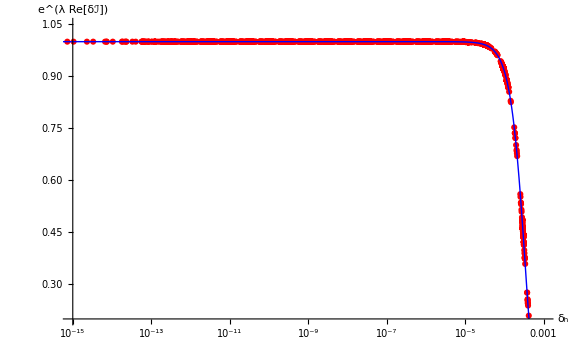

```mathematica
Show[ListPlot[thetaExpReS,ScalingFunctions->{"Log",None},PlotRange->{{10^-15,10^-3},{0.2,1.05}},PlotStyle->{Red,PointSize[0.02]},PlotMarkers->Automatic],Plot[Exp[10^11*f[x]],{x,10^-16,4.65*10^-1},ScalingFunctions->{"Log",None},PlotStyle->{Blue,Thick},PlotRange->{{10^-16,10^-4},{0.2,1.05}}],AxesLabel->{"δ_h","e^(λ Re[δℐ])"},AxesStyle->Thick,TicksStyle->Thick,ImageSize->Large,LabelStyle->Directive[Black,Bold,25],ImageSize->{600,600}]
```

### Contour plot of λ and δ_h(r)

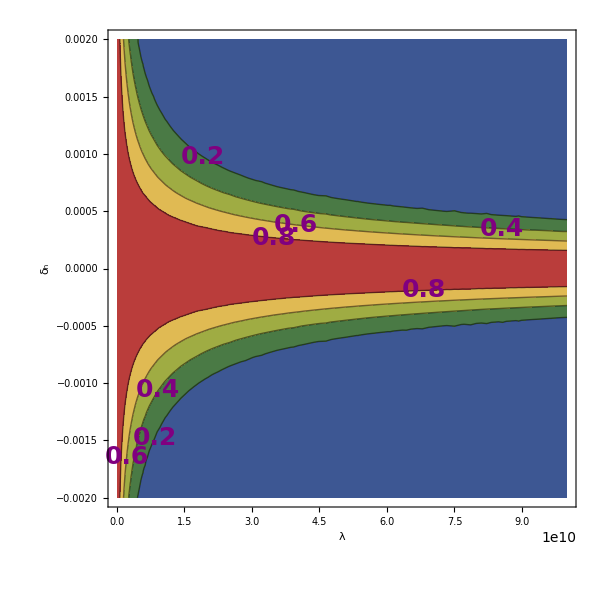

```mathematica
ContourPlot[Exp[λ*f[x]],{λ,10,10^11},{x,-2*10^-3,2*10^-3},ContourLabels->(Text[Style[#3,25,Purple,Bold],{#1,#2}]&),Contours->4,ContourStyle->Thick,Mesh->None,ColorFunction->"DarkRainbow",FrameLabel->{"λ","δ_h"},LabelStyle->Directive[Black,Bold,25],ImageSize->{600,600}]
```

### Contour plot of λ and γ

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"gammaData.wl"}]];
```

```mathematica
gamma={1/1000000,1/900000,1/800000,1/700000,1/600000,1/500000,1/400000,1/300000,1/200000,1/100000,1/90000,1/80000,1/70000,1/60000,1/50000,1/40000,1/30000,1/20000,1/10000,1/9000,1/8000,1/7000,1/6000,1/5000,1/4000,1/3000,1/2000,1/1000,1/900,1/800,1/700,1/600,1/500,1/400,1/300,1/200,1/100,1/90,1/80,1/70,1/60,1/50,1/40,1/30,1/20,1/10};
```

```mathematica
plotfunction=Interpolation[Flatten[Table[{list[[i,j,2,-1]],√(Total[Abs[list[[i,j,2,1]]]^2]/10),Re[list[[i,j,2,3]]]},{i,Length[gamma]},{j,Length[list[[i]]]}],1]]//N;
```

```mathematica
ContourPlot[Exp[λ*plotfunction[γ,x]]/.λ->5*10^10,{γ,10^-10,10^-2},{x,2*10^-6,3*10^-3},ContourLabels->(Text[Style[#3,25,Purple,Bold],{#1,#2}]&),Contours->{0.99,0.9,0.8,0.7,0.6,0.5},ContourStyle->Thick,Mesh->None,ColorFunction->"DarkRainbow",FrameLabel->{"γ","δ_h"},LabelStyle->Directive[Black,Bold,25],ImageSize->{600,600}]
```